```mathematica
(*Introduction*)
```

```mathematica
(*Syntax of Mathematica*)
```

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m;
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
(*Meaning of Expressions*)
```

```mathematica
FullForm[{a,b,c}]
```

List[a,b,c]

```mathematica
(*The Four Kinds of Bracketing in Mathematica*)
```

```mathematica
(* (term) Parentheses for groupung,
f[x]  square brackets for funcitons,
{a,b,c}  curly braces for lists,
v[[i]]  double brackets for indexing*)
```

```mathematica
(*How to use brackets and braces correctly*)
```

```mathematica
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"} (*Anything in Mathematica can be used in lists*)
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

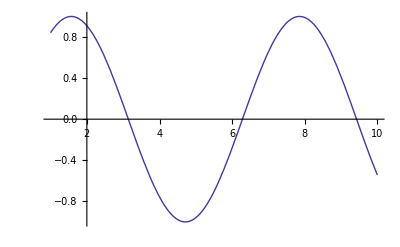

```mathematica
Plot[Sin[x],{x,1,10}]
```

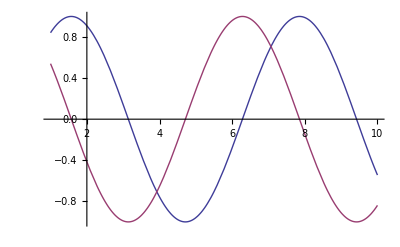

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*Symbolic Analysis*)
```

```mathematica
(*Symbolic Computation*)
```

```mathematica
-1+2 x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4 x^2
```

x-3 x^2

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*Values for symbols*)
```

```mathematica
1+2 x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x->3+y
```

x→3+y

```mathematica
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
Clear[x]
x=3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1+a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
(* x=.  removes any value defined for x *)
```

```mathematica
x+5-2 x
```

6+a-2 (1+a)

```mathematica
x=.
```

```mathematica
x+5-2 x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5 a
```

1+25 a^2

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
(* Transforming Algebraic Expressions *)
```

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[%]
```

-1+x^10

```mathematica
(* Simplifying Algebraic Expressions *)
```

```mathematica
Simplify[x^2+2 x+1]
```

(1+x)^2

```mathematica
Simplify[x^10-1]
```

-1+x^10

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x] (*Partial with respect to x*)
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x] Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x] Gamma[1-x]]
```

π Csc[π x]

```mathematica
(* 4. Calculus *)
```

```mathematica
(*Differentiation*)
```

```mathematica
D[x^n,x] (*Partial differentiation*)
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}] (*Third derivative*)
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
D[x^2+y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
D[x^2+y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
D[x^2+y^2,{{x,y}}] (*Gradient of x^2+y^2*)
```

{2 x,2 y}

```mathematica
D[x^2+y^2,{{x,y},2}]
```

{{2,0},{0,2}}

```mathematica
D[{x^2+y^2,x y},{{x,y}}] (*Jacobian*)
```

{{2 x,2 y},{y,x}}

```mathematica
(*Integration*)
```

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/(x^4-a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[Log[1-x^2]/x,x]
```

-1/2 PolyLog[2,x^2]

```mathematica
Integrate[Exp[1-x^2],x]
```

1/2 ⅇ √π Erf[x]

```mathematica
Integrate[x^x,x] (*Non-analytical integrals are left alone*)
```

∫x^x ⅆx

```mathematica
Integrate[Sin[x]^2,{x,a,b}] (*Definite integral*)
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
N[%] (*Numerical results*)
```

0.783431

```mathematica
Integrate[x^2+y^2,{x,0,1},{y,0,x}] (*Double integrals*)
```

1/3

```mathematica
Integrate[x^2,x] (*Indefinite integrals*)
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
D[%,x]
```

-1/(2 (1-x))-1/(2 (1+x))

```mathematica
Simplify[%]
```

1/(-1+x^2)

```mathematica
Integrate[x b[x]^2,b[x]]
```

1/3 x b[x]^3

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
(*Differential Equations*)
```

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

```mathematica
DSolve[y'[x]-y[x]^2==x,y[x],x]//FullSimplify
```

{{y[x]→(√x (-BesselJ[-2/3,(2 x^(3/2))/3]+BesselJ[2/3,(2 x^(3/2))/3] C[1]))/(BesselJ[1/3,(2 x^(3/2))/3]+BesselJ[-1/3,(2 x^(3/2))/3] C[1])}}

```mathematica
(*Plotting*)
```

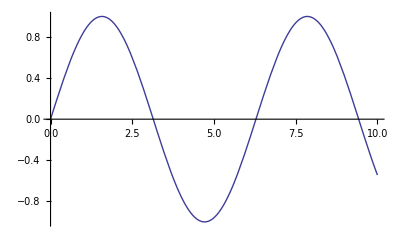

```mathematica
Plot[Sin[x],{x,0,10}]
```

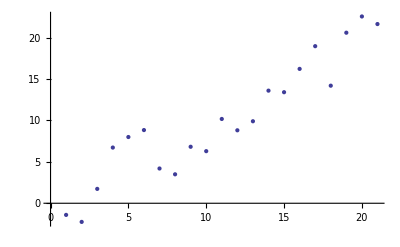

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]
```

-Graphics-

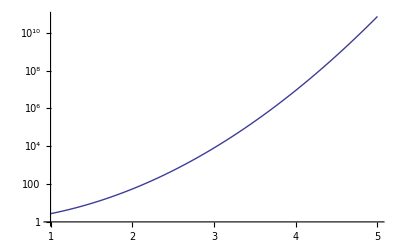

```mathematica
LogPlot[E^x^2,{x,1,5}]
```

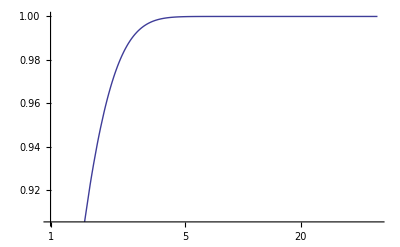

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

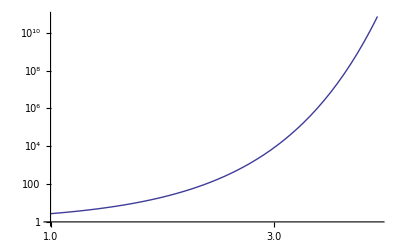

```mathematica
LogLogPlot[E^x^2,{x,1,5}]
```

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

```mathematica
(*Plotting results of NDSolve*)
```

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
```

```mathematica
sol=NDSolve[ode1,y,{x,-10,10}]
```

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

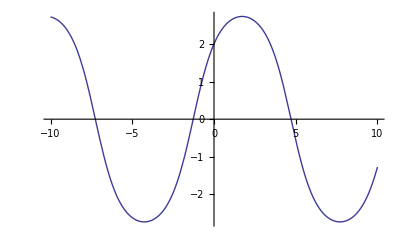

```mathematica
Plot[y[x]/.sol,{x,-10,10}]
```

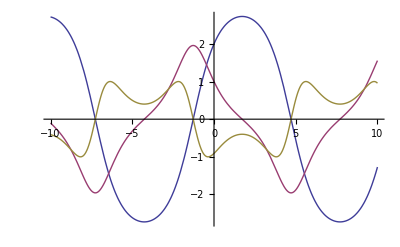

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}]
```

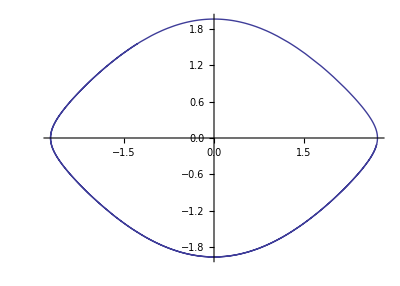

```mathematica
ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,-10,10}]
```

```mathematica
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

```mathematica
Plot3D[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

-Graphics3D-

```mathematica
(*Manipulate*)
```

```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]
```

```mathematica
Manipulate[Plot[a1 Sin[n1 (x+p1)]+a2 Sin[n2 (x+p2)],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{p1,0,2 Pi},{n2,1,20},{a2,0,1},{p2,0,2 Pi}]
```